```mathematica
saveFolder="/home/chengling/Research/Project/Cell/glassyDynamics/N4096/";
```

```mathematica
SISF=Table[Import[StringJoin[saveFolder,"SISF_N4096_p3.8000_T0.00337100_waitingTime3162.270000_idx",ToString[i],".nc"],"Data"],{i,0,2}];
```

```mathematica
SISF[[1,2,1]]
```

1.

```mathematica
chi4con=Table[4096*Table[Variance[Table[{SISF[[i,type,t]]},{i,3}]],{t, Length[SISF[[1,1]]]}],{type,2}];
```

```mathematica
ListLogPlot[Table]
```

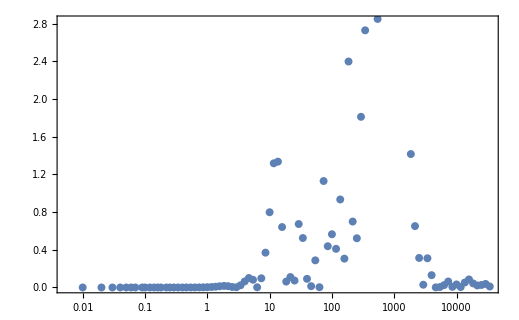

```mathematica
ListLogLinearPlot[Table[{N[test[[4,i,1]]-test[[4,1,1]]],chi4[[i,1]]},{i,Length[chi4]}]]
```

```mathematica
Table[{N[test[[4,i,1]]-test[[4,1,1]]],chi4[[i,1]]},{i,Length[chi4]}]
```

{{0.,0.},{0.01,8.02134×10^-15},{0.02,1.31677×10^-13},{0.03,6.83581×10^-13},{0.04,2.21385×10^-12},{0.05,5.53415×10^-12},{0.06,1.17408×10^-11},{0.07,2.2236×10^-11},{0.09,6.33414×10^-11},{0.1,9.84414×10^-11},{0.12,2.11562×10^-10},{0.14,4.044×10^-10},{0.16,7.08687×10^-10},{0.18,1.1609×10^-9},{0.22,2.67206×10^-9},{0.25,4.50369×10^-9},{0.29,8.12722×10^-9},{0.34,1.48437×10^-8},{0.4,2.60472×10^-8},{0.46,3.94455×10^-8},{0.54,5.62283×10^-8},{0.63,6.53641×10^-8},{0.74,5.62074×10^-8},{0.86,3.92551×10^-8},{1.,6.92247×10^-8},{1.17,2.27953×10^-7},{1.36,4.75769×10^-7},{1.58,5.94683×10^-7},{1.85,2.66297×10^-7},{2.15,4.8991×10^-7},{2.51,4.77458×10^-6},{2.93,0.0000136686},{3.41,0.0000181761},{3.98,0.0000148607},{4.64,0.0000137619},{5.41,0.000018468},{6.31,0.0000580868},{7.36,0.000120023},{8.58,0.000211203},{10.,0.000287838},{11.66,0.000152702},{13.59,0.0000615777},{15.85,0.0000309974},{18.48,4.18446×10^-6},{21.54,0.0000705768},{25.12,0.000261813},{29.29,0.000336274},{34.15,0.000412212},{39.81,0.000209167},{46.42,0.000016417},{54.12,0.0000183319},{63.1,0.000195928},{73.56,0.000133019},{85.77,0.0000255614},{100.,0.0000568563},{116.59,0.000344946},{135.94,0.00018808},{158.49,0.000402887},{184.78,0.000460515},{215.44,0.000333054},{251.19,0.0000575872},{292.86,0.000532464},{341.45,0.000115582},{398.11,0.000237543},{464.16,1.55343×10^-6},{541.17,0.000108942},{630.96,0.000217138},{735.64,0.00034638},{857.7,0.0000963525},{1000.,0.0000654056},{1165.91,0.000416384},{1359.36,3.30204×10^-6},{1584.89,0.0000176096},{1847.85,2.08907×10^-7},{2154.43,0.000166305},{2511.89,0.0000138395},{2928.64,0.0000917718},{3414.55,0.0000519381},{3981.07,0.0000365602},{4641.59,3.53335×10^-6},{5411.7,6.30842×10^-6},{6309.57,1.60209×10^-6},{7356.42,0.0000117779},{8576.96,9.11692×10^-7},{10000.,0.0000142557},{11659.1,1.54464×10^-9},{13593.6,6.72863×10^-7},{15848.9,9.77251×10^-6},{18478.5,0.0000169344},{21544.3,0.0000117065},{25118.9,5.69418×10^-6},{29286.4,3.78768×10^-6}}

```mathematica
data=Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/chi4CRchi4_N4096_p3.8000_T0.00337100_waitingTime3162.270000_idx1.nc","Data"]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

```mathematica
test=Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/glassyDynamics_N4096_p3.8000_T0.00337100_waitingTime1.000000_idx2.nc","Data"]
```

<|/BoxMatrix→NumericArray[…],/additionalData→NumericArray[<95,8192>, Real64],/postion→NumericArray[<95,8192>, Real64],/time→NumericArray[…],/type→NumericArray[<95,4096>, Integer32],/velocity→NumericArray[<95,8192>, Real64]|>

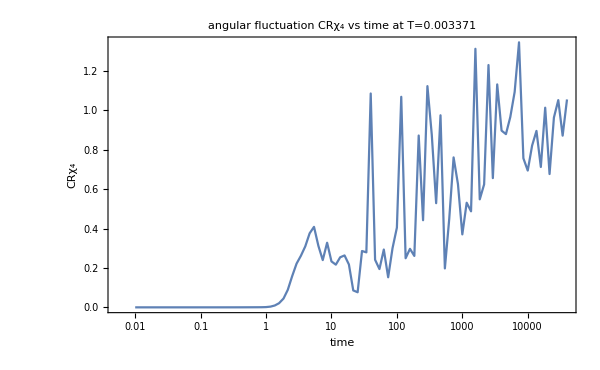

```mathematica
ListLogLinearPlot[Table[{N[test[[4,i,1]]-test[[4,1,1]]],data[[2,i]]},{i,Length[data[[1]]]-1}],FrameLabel->{"time","CRχ_4"},ImageSize->600,PlotLabel->"angular fluctuation CRχ_4 vs time at T=0.003371",Joined->True]
```

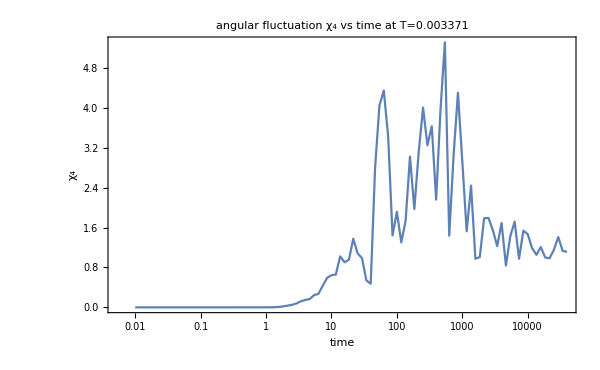

```mathematica
ListLogLinearPlot[Table[{N[test[[4,i,1]]-test[[4,1,1]]],data[[1,i]]},{i,Length[data[[1]]]-1}],FrameLabel->{"time","χ_4"},ImageSize->600,PlotLabel->"angular fluctuation χ_4 vs time at T=0.003371",Joined->True]
```

```mathematica
chi4ang=Table[Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/chi4CRchi4_N4096_p3.8000_T0.00337100_waitingTime3162.270000_idx"<>ToString[idx]<>".nc","Data"][[type]],{idx,0,2}],{type,2}];
```

```mathematica
Table[Mean[Table[chi4ang[[1,idx,i]],{idx,3}]],{i,Length[chi4ang[[1,1]]]}]
```

{0.,-9.74675×10^-11,1.18007×10^-9,6.03071×10^-9,1.9138×10^-8,4.67697×10^-8,9.5898×10^-8,1.76903×10^-7,4.74575×10^-7,7.17667×10^-7,1.46123×10^-6,2.65557×10^-6,4.43788×10^-6,6.95684×10^-6,0.0000148255,0.0000238352,0.0000410223,0.0000725554,0.00012798,0.000205383,0.000345978,0.000556689,0.000888264,0.00134522,0.00204169,0.00323724,0.00518856,0.00847449,0.0148779,0.0268434,0.0466551,0.0707078,0.0905213,0.0988293,0.10838,0.147065,0.251649,0.323482,0.3741,0.368236,0.567664,0.929225,0.924667,0.724678,1.44723,1.52477,2.40342,3.34513,2.03459,2.18821,3.36981,3.74842,3.9531,2.9478,2.64037,3.10744,5.24293,5.58432,4.11441,2.83943,3.13753,2.97566,4.01251,3.68818,4.52238,5.90027,2.83114,3.01812,3.31592,3.46198,3.35078,1.74096,1.54315,2.04779,1.97227,1.74658,1.85096,1.37519,1.53502,1.13461,1.60701,1.34348,1.13693,1.1546,1.24475,1.15129,1.17217,1.1081,0.928707,1.02952,1.0676,1.14237,0.978538}

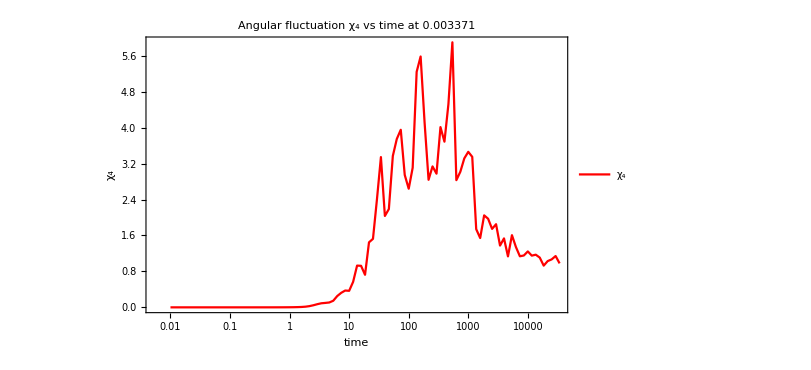

```mathematica
angChi4Plot=ListLogLinearPlot[Table[{N[test[[4,i,1]]-test[[4,1,1]]],Mean[Table[chi4ang[[1,idx,i]],{idx,3}]]},{i,Length[chi4ang[[1,1]]]}],FrameLabel->{"time","χ_4"},ImageSize->600,PlotLabel->"Angular fluctuation χ_4 vs time at 0.003371",Joined->True,PlotLegends->{"χ_4"},PlotStyle->redBluePlotConfig[2][[1]]]
```

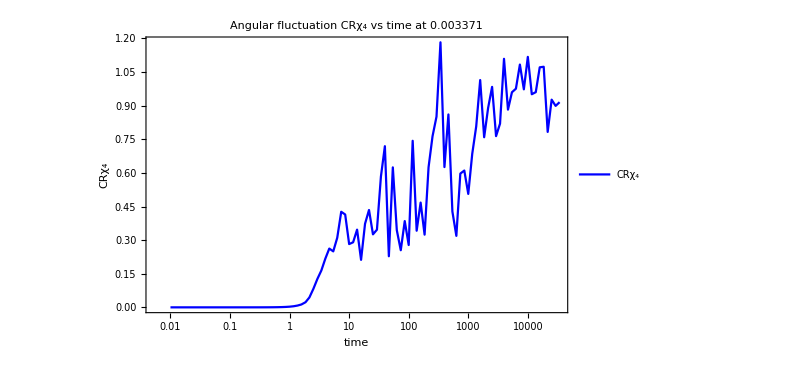

```mathematica
angCRChi4Plot=ListLogLinearPlot[Table[{N[test[[4,i,1]]-test[[4,1,1]]],Mean[Table[chi4ang[[2,idx,i]],{idx,3}]]},{i,Length[chi4ang[[1,1]]]}],FrameLabel->{"time","CRχ_4"},ImageSize->600,PlotLabel->"Angular fluctuation CRχ_4 vs time at 0.003371",Joined->True,PlotLegends->{"CRχ_4"},PlotStyle->Blue]
```

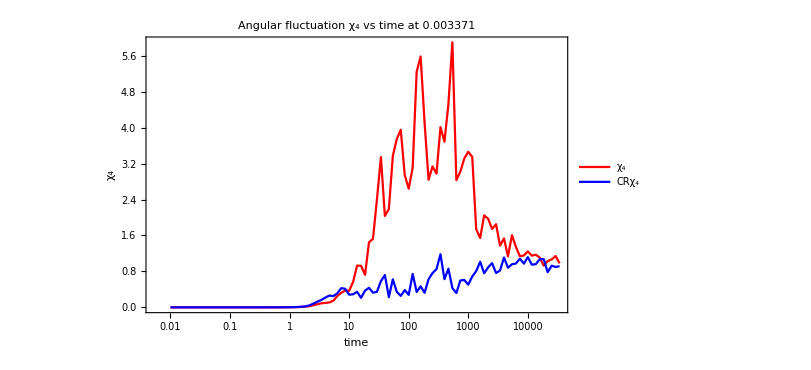

```mathematica
Show[angChi4Plot,angCRChi4Plot]
```

```mathematica
Export["/home/chengling/Research/updates/02012024/angularchi4.jpeg",Show[angChi4Plot,angCRChi4Plot],ImageResolution->600];
```

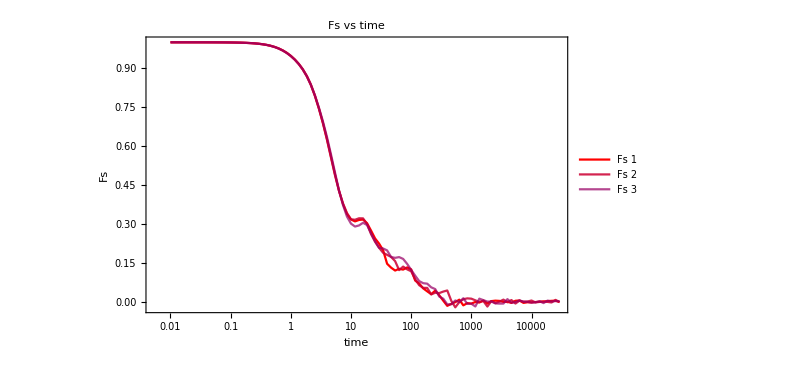

```mathematica
FsPlot=ListLogLinearPlot[Table[Table[{N[test[[4,i,1]]-test[[4,1,1]]],SISF[[idx,1,i]]},{i,Length[chi4]-1}],{idx,3}],FrameLabel->{"time","Fs"},ImageSize->600,PlotLabel->"Fs vs time",PlotStyle->redBluePlotConfig[6],PlotLegends->Table["Fs "<>ToString[i],{i,3}],Joined->True]
```

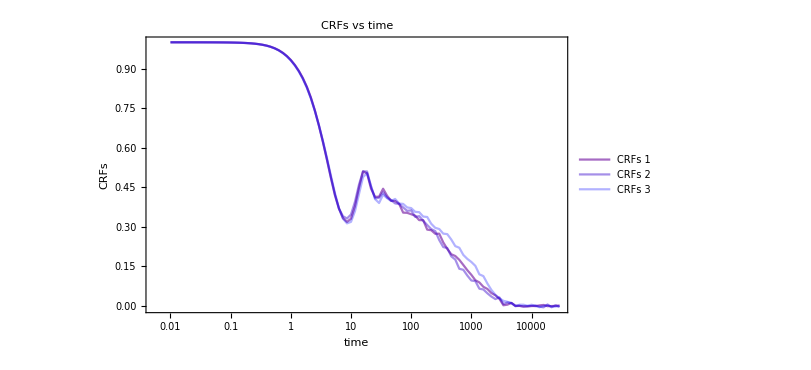

```mathematica
CRFsPlot=ListLogLinearPlot[Table[Table[{N[test[[4,i,1]]-test[[4,1,1]]],SISF[[idx,2,i]]},{i,Length[chi4]-1}],{idx,3}],FrameLabel->{"time","CRFs"},ImageSize->600,PlotLabel->"CRFs vs time",Joined->True,PlotStyle->redBluePlotConfig[6][[4;;]],PlotLegends->Table["CRFs "<>ToString[i],{i,3}]]
```

```mathematica
Export["/home/chengling/Research/updates/02012024/chi4Fs.jpeg",Show[FsPlot,CRFsPlot],ImageResolution->600];
```

```mathematica
chi4con[[1]]
```

{{0.},{6.18124×10^-11},{9.8715×10^-10},{4.98631×10^-9},{1.57185×10^-8},{3.82576×10^-8},{7.90457×10^-8},{1.45852×10^-7},{3.94914×10^-7},{5.98852×10^-7},{1.22813×10^-6},{2.24815×10^-6},{3.78605×10^-6},{5.98302×10^-6},{0.0000129768},{0.0000211502},{0.0000370643},{0.0000669677},{0.000120789},{0.000197308},{0.000336182},{0.000534724},{0.000801931},{0.00105702},{0.00124879},{0.0014457},{0.00202605},{0.00330206},{0.00477603},{0.00575169},{0.00837283},{0.0216051},{0.0620073},{0.125762},{0.175138},{0.125563},{0.00384263},{0.042961},{0.2058},{0.36917},{0.766022},{0.854786},{0.319303},{0.0506831},{0.202058},{0.195501},{0.354228},{0.282512},{2.81721},{2.32422},{2.64311},{3.13755},{1.85012},{0.469138},{0.0594525},{0.39006},{0.258876},{0.495324},{0.898987},{0.990435},{0.202505},{0.183411},{1.39449},{4.36681},{0.226105},{0.781471},{0.119367},{0.900067},{0.536766},{0.503319},{0.61415},{0.265458},{0.0128516},{0.381657},{0.00491195},{0.142762},{0.118258},{0.239604},{0.179177},{0.160584},{0.117731},{0.0018662},{0.0288117},{0.00810861},{0.0876221},{0.00231411},{0.00966412},{0.0487067},{0.0260891},{0.0410422},{0.0238011},{0.0204108},{0.00791781}}

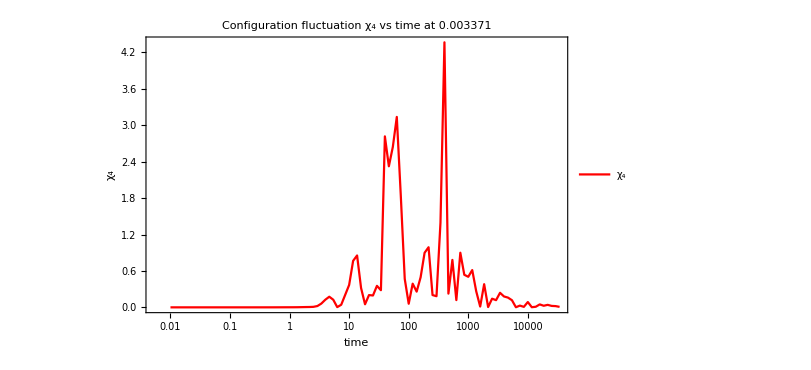

```mathematica
conChi4Plot=ListLogLinearPlot[Table[{N[test[[4,i,1]]-test[[4,1,1]]],chi4con[[1,i,1]]},{i,Length[chi4con[[1]]]}],FrameLabel->{"time","χ_4"},ImageSize->600,PlotLabel->"Configuration fluctuation χ_4 vs time at 0.003371",Joined->True,PlotRange->All,PlotStyle->redBluePlotConfig[2][[1]],PlotLegends->{"χ_4"},PlotRange->{Automatic,{0,7}}]
```

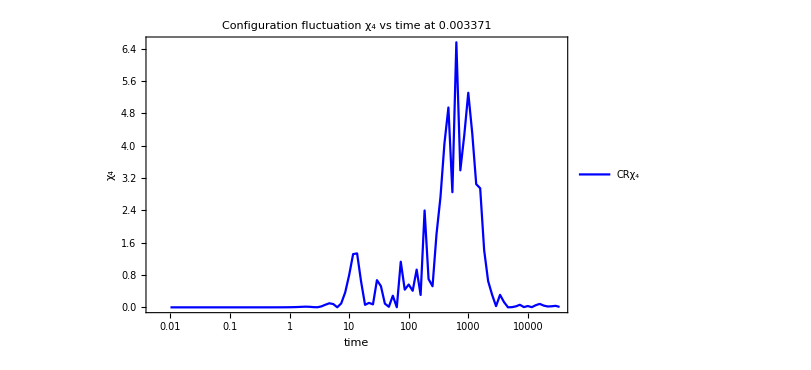

```mathematica
conCRChi4Plot=ListLogLinearPlot[Table[{N[test[[4,i,1]]-test[[4,1,1]]],chi4con[[2,i,1]]},{i,Length[chi4con[[1]]]}],FrameLabel->{"time","χ_4"},ImageSize->600,PlotLabel->"Configuration fluctuation χ_4 vs time at 0.003371",Joined->True,PlotRange->All,PlotStyle->Blue,PlotLegends->{"CRχ_4"}]
```

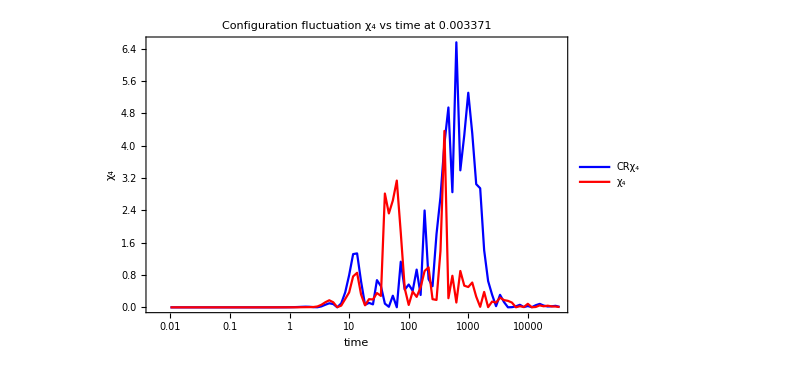

```mathematica
Show[conCRChi4Plot,conChi4Plot]
```

## High T CRchi4 from CRFs and CRoverlap

```mathematica
timeData=Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/chi4Test/N4096/chi4Test_N4096_p3.800_T0.01800000_5.nc","Data"]
```

<|/BoxMatrix→NumericArray[…],/additionalData→NumericArray[<90,8192>, Real64],/postion→NumericArray[<90,8192>, Real64],/time→NumericArray[…],/type→NumericArray[<90,4096>, Integer32],/velocity→NumericArray[<90,8192>, Real64]|>

```mathematica
timeData[[4]]
```

NumericArray[…]

```mathematica
time=Table[timeData[[4,i,1]]-timeData[[4,1,1]],{i,Length[timeData[[4]]]}]
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.13,0.14,0.16,0.18,0.2,0.22,0.25,0.28,0.32,0.35,0.4,0.45,0.5,0.56,0.63,0.71,0.79,0.89,1.,1.12,1.26,1.41,1.58,1.78,2.,2.24,2.51,2.82,3.16,3.55,3.98,4.47,5.01,5.62,6.31,7.08,7.94,8.91,10.,11.22,12.59,14.13,15.85,17.78,19.95,22.39,25.12,28.18,31.62,35.48,39.81,44.67,50.12,56.23,63.1,70.79,79.43,89.13,100.,112.2,125.89,141.25,158.49,177.83,199.53,223.87,251.19,281.84,316.23,354.81,398.11,446.68,501.19,562.34,630.96,707.95,794.33,891.25}

```mathematica
testdata=Import["/home/chengling/Research/Project/Cell/glassyDynamics/longtimeSimulation/N4096/glassyDynamics_N4096_p3.8000_T0.00181818_waitingTime100000.000000_idx2.nc","Data"];timeLong=Table[testdata[[4,j,1]]-testdata[[4,1,1]],{j,Length[testdata[[4]]]}]
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.09,0.1,0.12,0.14,0.16,0.18,0.22,0.25,0.29,0.34,0.4,0.46,0.54,0.63,0.74,0.86,1.,1.17,1.36,1.58,1.85,2.15,2.51,2.93,3.41,3.98,4.64,5.41,6.31,7.36,8.58,10.,11.66,13.59,15.85,18.48,21.54,25.12,29.29,34.15,39.81,46.42,54.12,63.1,73.56,85.77,100.,116.59,135.94,158.49,184.78,215.44,251.19,292.86,341.45,398.11,464.16,541.17,630.96,735.64,857.7,1000.,1165.91,1359.36,1584.89,1847.85,2154.43,2511.89,2928.64,3414.55,3981.07,4641.59,5411.7,6309.57,7356.42,8576.96,10000.,11659.1,13593.6,15848.9,18478.5,21544.3,25118.9,29286.4,34145.5,39810.7,46415.9,54117.,63095.7,73564.2,85769.6,100000.}

```mathematica
CRoverlapData=Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/chi4Test/N4096/CRoverlapCRchi4_special_N4096_p3.800_T0.01800000_"<>ToString[id]<>".nc","Data"],{id,0,100}];
```

```mathematica
Tlist={0.00309559, 0.00285428, 0.00264787 ,0.00246931, 0.0023133,0.00222222 ,0.00210526 ,0.002 ,0.00190476, 0.00181818};
```

```mathematica
Tstring=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist
```

{0.00309559,0.00285428,0.00264787,0.00246931,0.00231330,0.00222222,0.00210526,0.00200000,0.00190476,0.00181818}

```mathematica
mobilityC=Table[Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/longtimeSimulation/N4096/CRmobilityCorrelation_N4096_p3.8000_T"<>Tstring[[T]]<>"_"<>ToString[id]<>".nc","Data"][[2]],{id,0,2}],{T,Length[Tstring]}];
```

```mathematica
Normal[mobilityC[[1,1]]]
```

{0.,3.03458×10^-9,1.21128×10^-8,2.71897×10^-8,4.8211×10^-8,7.51134×10^-8,1.07824×10^-7,1.46263×10^-7,2.39951×10^-7,2.94994×10^-7,4.20893×10^-7,5.67003×10^-7,7.3216×10^-7,9.15077×10^-7,1.32817×10^-6,1.67295×10^-6,2.16821×10^-6,2.82359×10^-6,3.62459×10^-6,4.39485×10^-6,5.29456×10^-6,6.0457×10^-6,6.53799×10^-6,6.67415×10^-6,6.76554×10^-6,8.04979×10^-6,0.0000133287,0.0000273559,0.000058057,0.000108459,0.000188833,0.000290182,0.000370429,0.000400188,0.000420759,0.000520436,0.000569536,0.000536389,0.000563539,0.000257895,0.000261297,0.000181548,0.000148676,0.000265543,0.000184396,0.000266104,0.000365067,0.000342691,0.000123782,0.000264804,0.00043171,0.0003675,0.000521134,0.000378165,0.00135547,0.000687147,0.000100675,0.00110131,0.00170022,0.00117984,0.00123231,0.00147035,0.00122762,0.00127835,0.00346605,0.00238488,0.00147502,0.000640721,0.0023284,0.000168397,0.000253089,0.000176872,0.000944677,0.00146728,0.000486509,0.000850738,0.00228342,0.00177687,0.00429877,0.00275473,0.00228562,0.0016518,0.000300319,0.00236417,0.000307128,0.00215327,0.000545157,0.00379264,0.00161012,0.014541,0.0121354,0.0232544,0.0227348,0.0630965,0.102645,0.0281524,0.0756627,0.148583,0.22083,0.144619}

```mathematica
mobilityCMean=Table[Table[Mean[Table[mobilityC[[T,id,t]],{id,3}]],{t,Length[mobilityC[[T,1]]]}],{T,Length[Tstring]}];
```

```mathematica
CRoverlapDataSpecialVar=Table[Table[Variance[Table[CRoverlapDataSpecial[[T,id,t]],{id,3}]],{t,Length[CRoverlapDataSpecial[[T,1]]]}],{T,Length[Tstring]}];
```

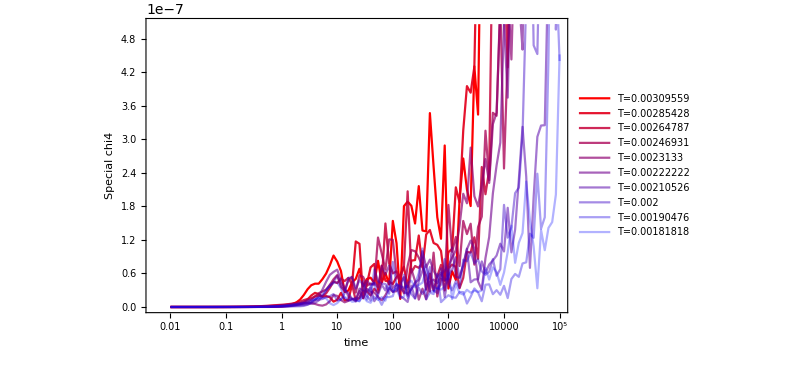

```mathematica
ListLogLinearPlot[Table[Table[{timeLong[[t]],1/4096*mobilityCMean[[T,t]]},{t,Length[mobilityCMean[[T]]]}],{T,Length[Tlist]}],FrameLabel->{"time","Special chi4"},ImageSize->600,PlotLabel->"",Joined->True,PlotStyle->redBluePlotConfig[10],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,10}]]
```

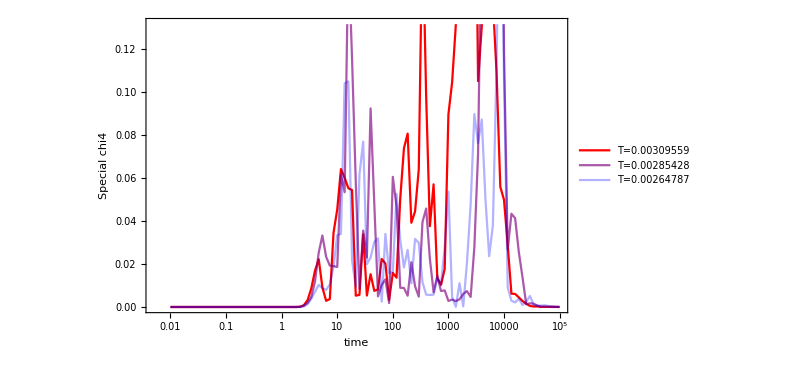

```mathematica
ListLogLinearPlot[Table[Table[{timeLong[[t]],1/4096*CRoverlapDataSpecialVar[[T,t]]},{t,Length[CRoverlapDataSpecialMean[[T]]]}],{T,3}],FrameLabel->{"time","Special chi4"},ImageSize->600,PlotLabel->"",Joined->True,PlotStyle->redBluePlotConfig[3],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,10}]]
```

```mathematica
tauAlphaCRSISF={1191.3693892697574,1967.8305026317012,2743.105691686508,4042.6497329224985,5138.480492118151,6673.482659784039,9274.507789022799,13129.797602048526,18585.09785778914,19030.103811663495}
```

{1191.37,1967.83,2743.11,4042.65,5138.48,6673.48,9274.51,13129.8,18585.1,19030.1}

```mathematica
peakX={833.0669145143971,1184.8254955455707,1528.0444131206045,2173.253969696539,3214.268505712585,4065.043111278644,5451.850138394158,7031.135957542836,9616.185509086494,11925.792594822462}
```

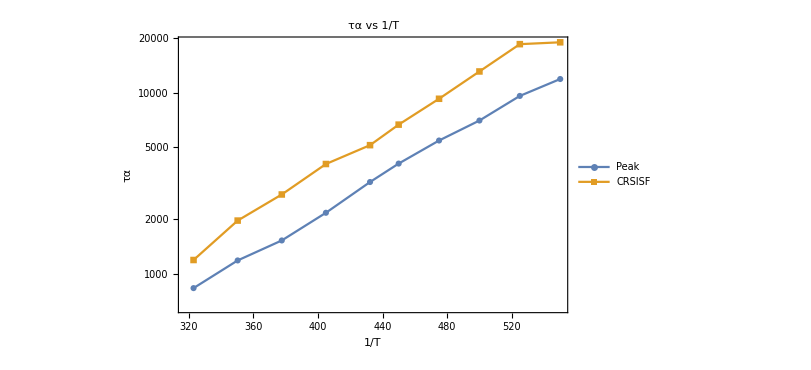

```mathematica
ListLogPlot[{Table[{1/Tlist[[T]],peakX[[T]]},{T,Length[Tlist]}],Table[{1/Tlist[[T]],tauAlphaCRSISF[[T]]},{T,Length[Tlist]}]},FrameLabel->{"1/T","τα"},PlotLegends->{"Peak","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"τα vs 1/T",Joined->True,PlotRange->All]
```

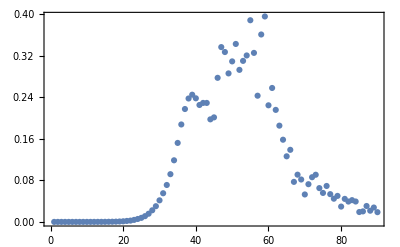

```mathematica
ListPlot[4096*Table[Variance[Table[CRoverlapData[[i,t]],{i,40}]],{t,Length[CRoverlapData[[1]]]}]]
```

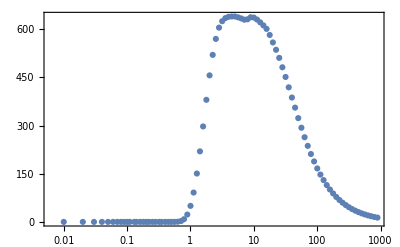

```mathematica
ListLogLinearPlot[Table[{time[[t]],Mean[Table[CRoverlapData[[i,2,t]],{i,101}]]},{t,Length[CRoverlapData[[1,1]]]}],PlotRange->All]
```

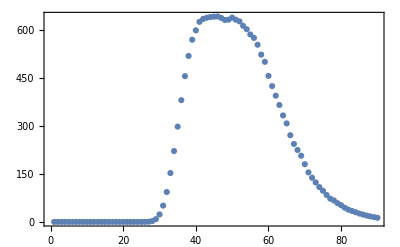

```mathematica
ListPlot[Normal[CRoverlapData[[1,2]]]-1]
```

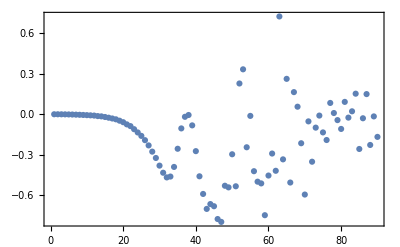

```mathematica
ListPlot[Normal[CRoverlapData[[1,2]]]-1+Table[CRoverlapData[[1,1,t]]^2,{t,Length[CRoverlapData[[1,1]]]}]]
```

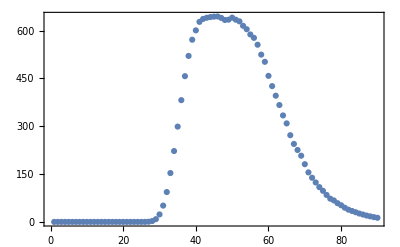

{1.,0.999918,0.999672,0.999263,0.99869,0.997955,0.997059,0.996001,0.994783,0.993406,0.991871,0.990179,0.986331,0.984177,0.979419,0.974071,0.96815,0.961673,0.950954,0.939092,0.921624,0.907386,0.881734,0.854029,0.824678,0.787859,0.743552,0.692338,0.641705,0.580659,0.517663,0.454886,0.390027,0.330258,0.27327,0.218362,0.170102,0.129385,0.0958181,0.0694736,0.0508395,0.0381547,0.0313415,0.0287861,0.0297923,0.0338748,0.0396147,0.0449913,0.0454542,0.0354643,0.0244085,0.0175868,0.0144355,0.0135728,0.0105965,0.00666902,0.00496352,0.00299822,0.00259123,0.00120212,0.00082815,0.000558314,0.000139664,5.0874×10^-6,0.0000744206,1.29197×10^-7,0.0000492493,1.22111×10^-6,7.40871×10^-6,3.60253×10^-6,6.76436×10^-7,0.0000615757,8.93367×10^-6,0.000109553,4.86945×10^-6,6.66965×10^-6,0.000036178,6.40548×10^-6,2.25968×10^-6,1.30098×10^-6,3.17747×10^-8,4.61818×10^-7,4.30437×10^-7,0.0000198499,2.23336×10^-6,4.12204×10^-6,9.43044×10^-6,0.0000239777,8.02351×10^-9,7.07043×10^-6}

```mathematica
ListPlot[Table[CRoverlapData[[1,2,t]],{t,Length[CRoverlapData[[1,1]]]}]]
```

```mathematica
random=RandomInteger[{0,1},1000];
```

```mathematica
randMean=Mean[random]
```

483/1000

```mathematica
Total[Total[Table[Table[(random[[i]]-randMean)*(random[[j]]-randMean),{i,Length[random]}],{j,Length[random]}]]]
```

0

## configurational chi4

```mathematica
CRoverlapData=Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/chi4Test/N4096/CRoverlapCRchi4_special_N4096_p3.800_T0.01800000_"<>ToString[id]<>".nc","Data"][[1]],{id,0,100}];
```

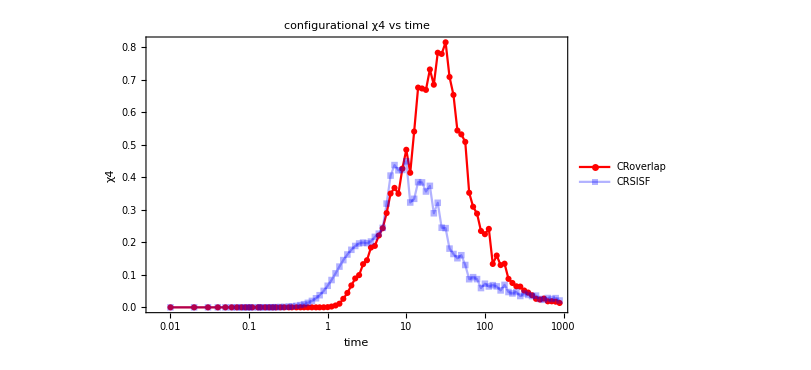

```mathematica
ListLogLinearPlot[{Table[{time[[t]],4096*Variance[Table[CRoverlapData[[i,t]],{i,101}]]},{t,Length[CRoverlapData[[1]]]}],Table[{time[[t]],4096*Variance[Table[CRSISFData[[i,t]],{i,101}]]},{t,Length[CRoverlapData[[1]]]}]},FrameLabel->{"time","χ4"},PlotLegends->{"CRoverlap","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"configurational χ4 vs time",Joined->True,PlotStyle->redBluePlotConfig[2]]
```

```mathematica
Export["/home/chengling/Research/updates/02082024/conchi4.jpeg",ListLogLinearPlot[{Table[{time[[t]],4096*Variance[Table[CRoverlapData[[i,t]],{i,101}]]},{t,Length[CRoverlapData[[1]]]}],Table[{time[[t]],4096*Variance[Table[CRSISFData[[i,t]],{i,101}]]},{t,Length[CRoverlapData[[1]]]}]},FrameLabel->{"time","χ4"},PlotLegends->{"CRoverlap","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"configurational χ4 vs time",Joined->True,PlotStyle->redBluePlotConfig[2]],ImageResolution->600];
```

```mathematica
CRSISFData=Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/chi4Test/N4096/CRFsCRchi4_N4096_p3.800_T0.01800000_"<>ToString[id]<>".nc","Data"][[1]],{id,0,100}];
```

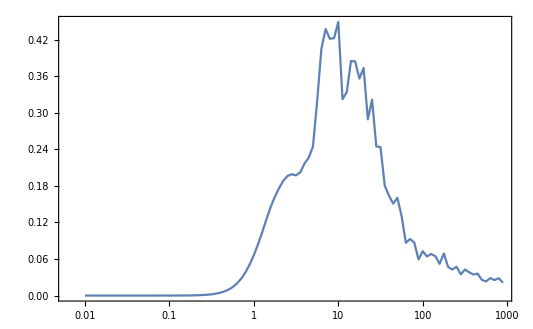

```mathematica
ListLogLinearPlot[Table[{time[[t]],4096*Variance[Table[CRSISFData[[i,t]],{i,101}]]},{t,Length[CRoverlapData[[1]]]}],Joined->True]
```

```mathematica
AngularChi4Data=Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/chi4Test/N4096/CRFsCRchi4_N4096_p3.800_T0.01800000_"<>ToString[id]<>".nc","Data"][[2]],{id,0,100}];
```

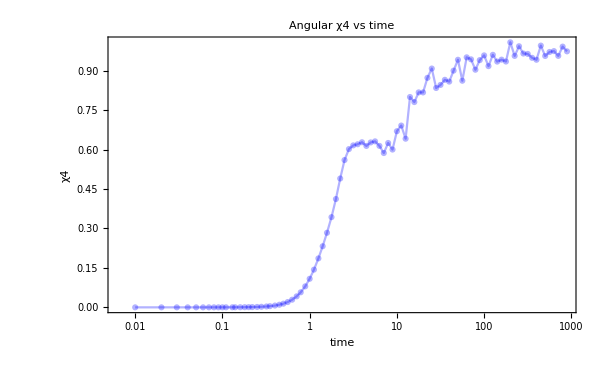

```mathematica
ListLogLinearPlot[Table[{time[[t]],Mean[Table[AngularChi4Data[[i,t]],{i,101}]]},{t,Length[CRoverlapData[[1]]]}],FrameLabel->{"time","χ4"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"Angular χ4 vs time",Joined->True,PlotStyle->redBluePlotConfig[2]]
```

```mathematica
Export["/home/chengling/Research/updates/02082024/angchi4.jpeg",ListLogLinearPlot[Table[{time[[t]],Mean[Table[AngularChi4Data[[i,t]],{i,101}]]},{t,Length[CRoverlapData[[1]]]}],FrameLabel->{"time","χ4"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"Angular χ4 vs time",Joined->True,PlotStyle->redBluePlotConfig[2]],ImageResolution->600];
```

```mathematica
qs=RandomInteger[{0,1},1000];
```

```mathematica
N[Variance[qs]]
```

0.250054